```mathematica
SetDirectory@NotebookDirectory[]
```

C:\GitHub\fastm\test

```mathematica
gabs={{-1.2,-0.2},{1.2,0.2}};
```

```mathematica
h=0.04;
```

```mathematica
pts=Flatten[Table[{0.000123,0.000456}+{x,y},{x,gabs[[1,1]],gabs[[2,1]],h},{y,gabs[[1,2]],gabs[[2,2]],h}],1];
```

```mathematica
Export["vp"<>ToString[Length@pts]<>".txt",{Length@pts}~Join~pts,"Table"]
```

vp671.txt

```mathematica
velCalc=Import["../res/velBSWing128.txt","Table"];
```

```mathematica
cft=0.01;
```

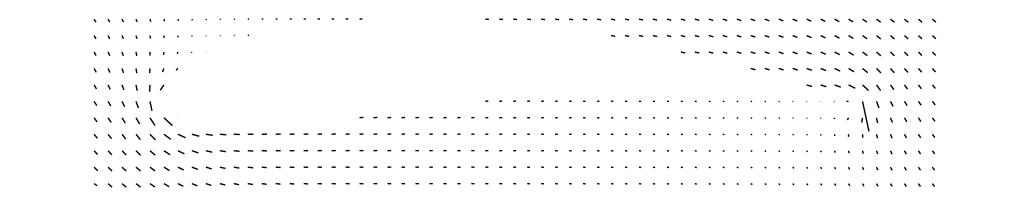

```mathematica
Graphics[Table[Line[{pts[[i]],pts[[i]]+cft velCalc[[i]]}],{i,Length@pts}]]
```